```mathematica
Kappa[n_] := N[MangoldtLambda[n]/Log[n]]
F[n_, p_, k_] :=F[n,p,k]= Sum[ Kappa[j] p( 1/(k!) + F[Floor[n/j],p,k+1]),{j,2,n}]
FF[n_,p_] := 1+F[n,p,1]
G[n_,p_,k_] := G[n,p,k] = Sum[ Kappa[j]( p^k/(k!) - G[Floor[n/j],p,k+2]),{j,2,n}]
GG[n_,p_] := G[n,p,1]
H[n_,p_,k_] := H[n,p,k] = Sum[ Kappa[j]( p^k/(k!) - H[Floor[n/j],p,k+2]),{j,2,n}]
HH[n_,p_] := 1+H[n,p,2]
```

```mathematica
H[100,1,1]
```

14.4652

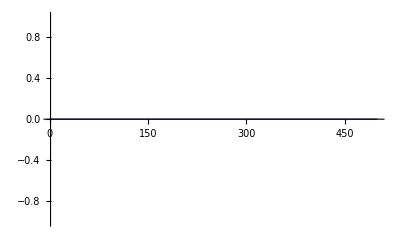

-Graphics-

```mathematica
DiscretePlot[GG[n,1]+GG[n,-1],{n,1,500}]
DiscretePlot[HH[n,1]-HH[n,-1],{n,1,500}]
```

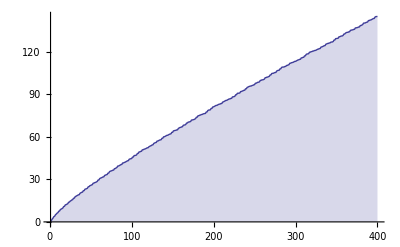

```mathematica
DiscretePlot[Im[GG[n,I]],{n,1,400}]
```

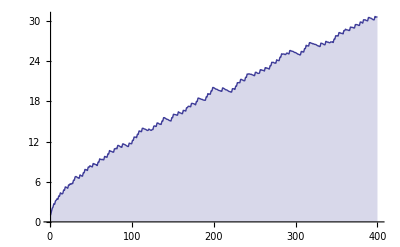

```mathematica
DiscretePlot[HH[n,1],{n,1,400}]
```

```mathematica
HH[100,I]
```

-17.2122

```mathematica
FF[100,3I]
```

-69.625-405.125 ⅈ

```mathematica
GG[100,3]
```

-112.674

```mathematica
HH[100,3]
```

-66.3755